# Radial Basis Function

We have found out that meshing things is a pain.  We are going to do a brief intro to a meshless method based on Radial Basis Functions.

## Interpolation: Implementation

Suppose we have a bunch of points on a surface in 3D and want to run a “nice” function through them.

Our points are going to be p_1,p_2,...,p_n are a list of points in 2D with matching heights u_1,u_2,…,u_n.

These methods are based on approximating functions using radial functions like 
	ϕ(r)=E^(-(r/ϵ)^2)
where ϵ is a length scale that we will have to pick and r is the distance from a point. 
The RBF idea is to look for a “fitting” function of the form 
	v[{x_1,x_2}]=∑_(i=1)^n a_i ϕ(|{x_1,x_2}-p_i|)
where the centers are the n points in 2D p_1,p_2,...,p_n and we need to find the coefficients a_1,…,a_n. We simply enforce the interpolation conditions
	v[p_j]=∑_(i=1)^n a_i ϕ(|p_j-p_i|)=u_j  for j=1…n
to get n linear equations for the vector a.  Of course real implementations involve some details! Here is a simple version!

### Points and Overview

We pick a domain, a bunch of points in it, and a synthetic function.  Our target is to recreate something that looks like the function from the data.  This is an “interpolation” problem.

```mathematica
Omega=DiscretizeRegion[Disk[{0,0},1],MaxCellMeasure->0.1];
Pts=MeshCoordinates[Omega]; n=Length[Pts];
ListPlot[Pts,AspectRatio->Automatic];
uSol[{x1_,x2_}]:= Cos[x1+ E^x1 Sin[x1+  x2]]
u=Table[uSol[Pts⟦i⟧],{i,n}];
n=Length[Pts];
ThreeDPoints=Table[{x1,x2}=Pts⟦i⟧;
{x1,x2,u⟦i⟧},{i,1,Length[Pts]}];
Pic1=Show[
ListPointPlot3D[ThreeDPoints,PlotStyle->Green],
Plot3D[uSol[{x1,x2}],{x1,x2}∈Omega]
]
```

-Graphics3D-

We are going to use the “Gaussian” shape function
	ϕ(r)=E^(-(r/ϵ)^2)
and the RBF representation 
	v(x) = ∑_(i=1)^n a_i ϕ(|x-p_i|)
where n is the number of points.  Plugging each point p_j into v gives a different linear equation.  All we need to do is build the equations then write them as a linear system 
	A.a=b,
solve the linear system for a, and finally assemble and plot v({x_1,x_2}).

I define the Gaussian shape function ϕ(r)=E^(-(r/ϵ)^2) to build our interpolation equations. Plugging in p_j we want
	 v(p_j)=∑_(i=1)^(n+m) a_i ϕ(|p_i-p_j|)=u_j
for j=1,...,n.  The equations only involve the distances r_(i,j)=r_(j,i)=|p_i-p_j|. The first equation is
	ϕ[r_(1,1)]a_1+ϕ[r_(1,2)]a_2+…+ϕ[r_(1,n)]a_n=u_1.
The other equations follow the same pattern. The first equation is the first row of the matrix.  The other row follow the same pattern!

### Building Matrices

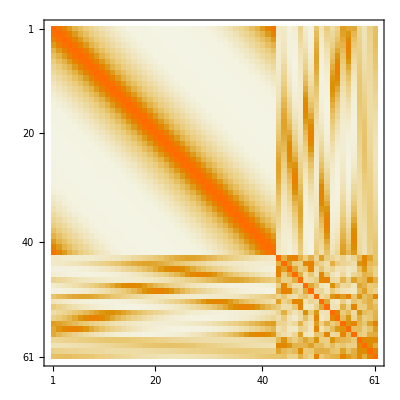

```mathematica
ϕ[ϵ_][r_]:= E^(-(r/ϵ)^2)
rS=Table[
Norm[Pts⟦i⟧-Pts⟦j⟧],
{i,1,n},
{j,1,n}];
ϵ=0.4;
A= Table[ϕ[ϵ][rS⟦i,j⟧],{i,1,n},{j,1,n}];
MatrixPlot[A]
```

We need to solve the linear system. The bad news is that these are not easy to interpret nodal values.

```mathematica
a=LinearSolve[A,u];
v[p_]:= Sum[a⟦i⟧ ϕ[ϵ][Norm[p-Pts⟦i⟧]],{i,1,n}]
Show[
Pic1,
Plot3D[v[{x1,x2}],
{x1,x2}∈Omega,
PlotStyle->LightBlue]
]
```

-Graphics3D-

Putting it all together with more points.

```mathematica
Omega=DiscretizeRegion[Disk[{0,0},1],MaxCellMeasure->0.025];
Pts=MeshCoordinates[Omega]; n=Length[Pts];
uSol[{x1_,x2_}]:= Cos[x1+ Sin[x1  x2]]
u=Table[uSol[Pts⟦i⟧],{i,n}];
ThreeDPoints=ArrayFlatten[({{Pts, {u}ᵀ}})];
A= ϕ[ϵ_][r_]:= E^(-(r/ϵ)^2)
ϵ=0.4;
A= Table[ϕ[ϵ][Norm[Pts⟦i⟧-Pts⟦j⟧]],{i,n},{j,n}];
a=LinearSolve[A,u];
v[p_]:= Sum[a⟦i⟧ ϕ[ϵ][Norm[p-Pts⟦i⟧]],{i,1,n}]
Show[
ListPointPlot3D[ThreeDPoints,PlotStyle->Green],
Plot3D[{uSol[{x1,x2}],v[{x1,x2}]},{x1,x2}∈Omega]
]
```

-Graphics3D-

```mathematica
ContourPlot[uSol[{x1,x2}]-v[{x1,x2}],{x1,x2}∈Omega,
PlotRange->All,
PlotPoints->123,
PlotLegends->Automatic]
```

-Graphics-

## Poisson Equation: Implementation

These methods are based on approximating functions using radial functions like 
	ϕ(r)=E^(-(r/ϵ)^2)
where ϵ is a length scale that we will have to pick and r is the distance from a point. 
Lets make this more explicit.  As always, for our first we are going to try to solve 
	Δu=f
on some bounded domain Ω⊂ℝ^2 with Dirichlet boundary conditions on ∂Ω.  We have a bunch of interior points 
	{p_1,p_2,…,p_n}ϵ Ω
and a bunch of boundary points 
	{p_(n+1),p_(n+2),…,p_(n+m)}ϵ Ω.
Since we have Dirichlet conditions we know u(p_i) for i=n+1,…,n+m.   
RBF means we decide to look for an approximate solution of the form 
	v[{x_1,x_2}]=∑_(i=1)^(n+m) a_i ϕ(|{x_1,x_2}-p_i|)
There are n+m scalar unknowns in this expression.  We need n+m equations to solve for the vector a! 
We get n equations by requiring that -Δv(p_j)=f(p_i) for i=1,...,n.  
We get m equations by requiring that v(p_i)=u(p_i) for i=n+1,...,n+m.  BC gives u(p_i).
Assembling gives a square linear system of n+m equations. 
Of course real implementations involve lots of details! Here is the simplest possible version!

### Points and Overview

We pick a domain and a bunch of points in it

{19,42}

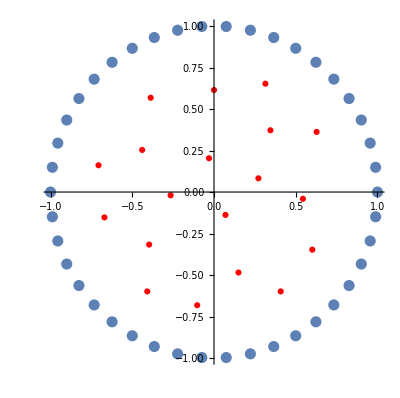

```mathematica
Omega=DiscretizeRegion[Disk[{0,0},1],MaxCellMeasure->0.1];
Pts=MeshCoordinates[Omega];
δ=0.0001;
dirichletPoints=Select[Pts,(Norm[#]>1-δ)&];
innerPoints = Complement[Pts,dirichletPoints];
{n,m}=Map[Length,{innerPoints,dirichletPoints}]
Pts=Join[innerPoints,dirichletPoints];
ListPlot[{dirichletPoints,innerPoints},
PlotStyle->{PointSize[0.02],Red},
AspectRatio->Automatic]
```

Plugging each edge point into v gives a linear equation.  Computing the Laplacian of v and plugging in each inner point gives a linear equation. All we need to do is build these equations and convert them into a linear system 
	A.a=b,
solve the linear system, and finally assemble and plot v({x_1,x_2}).

### Shape Functions

Our v is the sum of functions ϕ(|{x_1,y_1}-p|)  where p is one of the two dimensional node points. We need a recipe for the Laplacian of each of these functions.  For simplicity we focus purely on the the Gaussian shape function
	ϕ(r)=E^(-(r/ϵ)^2)
With r=√(x^2+y^2) the Laplacian of ϕ(r) is pretty clean.  In fact,  it is simply
	(4 E^(-(r/ϵ)^2) (r^2-ϵ^2))/ϵ^4

```mathematica
Clear[ϵ]
Simplify[Laplacian[ E^(-(x^2+y^2)/ϵ^2),{x,y}]]/.{x^2+y^2->r^2}
```

(4 ⅇ^(-r^2/ϵ^2) (r^2-ϵ^2))/ϵ^4

If we write 
	ϕ_i(x)=ϕ(r_i)  where r_i=|x-p_i|
then 
	Δϕ_i(x)=ψ_i(x)=ψ(r_i)  where ψ=4E^(-(r/ϵ)^2)(r^2/ϵ^4-ϵ^-2)
and v  looks cleaner
	v(x) = ∑_(i=1)^(n+m) a_i ϕ_i(x)
and so does 
	Δv(x)=∑_(i=1)^(n+m) a_i Δϕ_i(x)=∑_(i=1)^(n+m) a_i ψ_i(x).

We can now build our equations.

The first n points p_1,...,p_n are interior points. Plugging in p_j we need
	 Δv(p_j)=∑_(i=1)^(n+m) a_i ψ_i(p_j)=f(p_j)
for j=1,...,n.

The next m points p_(n+1),...,p_(n+m) are boundary points. Plugging in p_j we need
	 v(p_j)=∑_(i=1)^(n+m) a_i ϕ_i(p_j)=u(p_j)
for j=n+1,...,n+m.

Everything is determined by the distances r_(i,j)=|p_i-p_j|

### Building Matrices

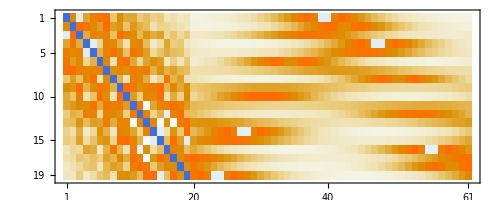

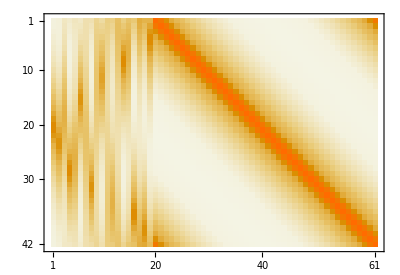

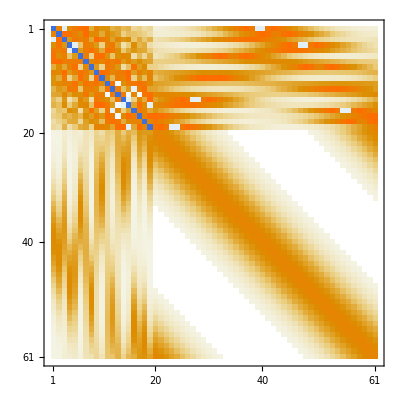

```mathematica
ϕ[ϵ_][r_]:= E^(-(r/ϵ)^2)
ψ[ϵ_][r_]:= 4 E^(-(r/ϵ)^2)(r^2/ϵ^4-ϵ^-2)
Simplify[Laplacian[Simplify[ϕ[ϵ][√(x1^2+x2^2)]],{x1,x2}]-ψ[ϵ][√(x1^2+x2^2)]];
rS=Table[
Norm[Pts⟦i⟧-Pts⟦j⟧],
{i,1,n+m},
{j,1,n+m}];
ϵ=0.3;
AInner= Table[
ψ[ϵ][rS⟦i,j⟧],{j,1,n},{i,1,n+m}];
ADirichlet = Table[ϕ[ϵ][rS⟦i,j⟧],{j,n+1,n+m},{i,1,n+m}];
MatrixPlot[AInner]
MatrixPlot[ADirichlet]
A=Join[AInner,ADirichlet];
MatrixPlot[A]
```

### Building RHS and Solving

We choose an answer u and construct a problem with that as an answer.  This is what we have been calling a synthetic solution.  The Dirichlet boundary condition is just the answer evaluated on the boundary and we choose the f to satisfy the PDE 
	Δu=f
In other words we pick f to be the Laplacian of our synthetic solution.

```mathematica
Clear[uSol,x1,x2]
uSol[{x1_,x2_}]:= Cos[x1+ Sin[x1  x2]]
f[{x1_,x2_}]= Laplacian[uSol[{x1,x2}],{x1,x2}];
b=Join[
Table[f[Pts⟦j⟧],{j,1,n}],
Table[uSol[Pts⟦j⟧],{j,n+1,n+m}]];
a=LinearSolve[A,b];
v[p_]:= Sum[a⟦i⟧ ϕ[ϵ][Norm[p-Pts⟦i⟧]],{i,Length[Pts]}]
Show[
Plot3D[{uSol[{x1,x2}],v[{x1,x2}]},{x1,x2}∈Omega]
]
```

-Graphics3D-

### Putting it all together with higher resolution

-Graphics3D-

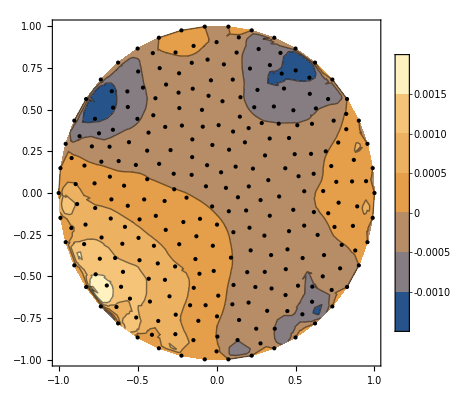

```mathematica
Omega=DiscretizeRegion[Disk[{0,0},1],MaxCellMeasure->0.01];
Pts=MeshCoordinates[Omega];
δ=0.0001;dirichletPoints=Select[Pts,(Norm[#]>1-δ)&];
innerPoints = Complement[Pts,dirichletPoints];
{n,m}=Map[Length,{innerPoints,dirichletPoints}];
Pts=Join[innerPoints,dirichletPoints];
ϕ[ϵ_][r_]:= E^(-(r/ϵ)^2)
ψ[ϵ_][r_]:= 4 E^(-(r/ϵ)^2)(r^2/ϵ^4-ϵ^-2)
ϵ=0.3;
A=Join[
Table[ψ[ϵ][Norm[Pts⟦i⟧-Pts[[j]]]],{j,1,n},{i,1,n+m}],
Table[ϕ[ϵ][Norm[Pts⟦i⟧-Pts[[j]]]],{j,n+1,n+m},{i,1,n+m}]];
Clear[uSol,x1,x2]
uSol[{x1_,x2_}]:= Cos[x1^2+ Sin[x1  x2]-x2]
f[{x1_,x2_}]= Laplacian[uSol[{x1,x2}],{x1,x2}];
b=Join[
Table[f[Pts⟦j⟧],{j,1,n}],
Table[uSol[Pts⟦j⟧],{j,n+1,n+m}]];
a=LinearSolve[A,b];
v[p_]:= Sum[a⟦i⟧ ϕ[ϵ][Norm[p-Pts⟦i⟧]],{i,Length[Pts]}]
Plot3D[{uSol[{x1,x2}],v[{x1,x2}]},{x1,x2}∈Omega,
PlotRange->All]
ContourPlot[uSol[{x1,x2}]-v[{x1,x2}],{x1,x2}∈Omega,
PlotLegends->Automatic,
Epilog->Map[Point,Pts⟦All,{1,2}⟧]]
```